## Gaussian beam propagation

P.Huft

## Setup

import functions for Gaussian beams, propagation, etc.

```mathematica
SetDirectory[NotebookDirectory[]];
<<"optics.m"
```

Guassian beam parameters:

## Propagate and plot the beam

### Waist transformation

check the relation w1w2 = λf/π, where w1,w2 are the full waists in the front and back focal plane of a lens with focal length f.

```mathematica
λ = 4.8*^-7;
inputWaist = {3.5*^-5,5*^-5}; (*system input waists wx,wy*)
colors = {Red,Green}; (*colors of waist plot lines*)
legends=Table[StringForm["``mm",waist/10^-3],{waist,inputWaist}];
f1 = .008; (*[m] lens focal length*)
lenses = {(*the system of optics*)
{IdentityMatrix[2],f1},
{MLens[f1],f1}};
```

```mathematica
waistfuncs ={};
For[i=1,i<Length[inputWaist]+1,i++,
q0 = -ⅈ π inputWaist[[i]]^2/λ;
AppendTo[waistfuncs,beamPropagate[q0,lenses,λ]](*system input beam*)
]
```

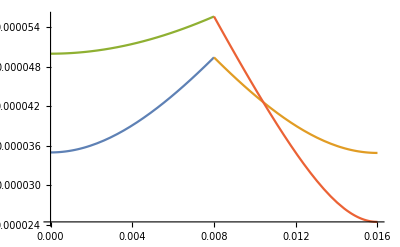

```mathematica
Plot[Evaluate[waistfuncs],{x,0,f1+f1},PlotRange->All]
```

```mathematica
(waistfuncs[[1,1]]/.x->10^-10)(waistfuncs[[1,2]]/.x->2f1)-(λ f1)/π
```

0.

```mathematica
(waistfuncs[[2,1]]/.x->10^-10)(waistfuncs[[2,2]]/.x->2f1)-(λ f1)/π
```

-2.06795×10^-25